# Homework assignment 4

Kyle McGraw <kmcgraw@caltech.edu>

I worked for >>6 hours on this set and spend a couple hours just on inverse and division trying to test and figure out a way to do these functions. I was having some issues and they don’t work perfectly, but this is what I was able to complete without spending an unreasonable amount of time on this project. Unfortunately, I had done the most of the rest of the set earlier in the week except for the last few functions, and had other work so wasn’t able to go to office hours or get help. In the future, I’ll make sure to look through all the functions to make sure I get my questions answered earlier in the week.

## Part 1: Systematic construction of a CRN with chaotic dynamics.

Chaotic Rössler attractor:                                                
	           dx/dt=-z-y 
	           dy/dt=x+a y
	           dz/dt=b+z (x-c)
These differential equations are turned into dual rail by taking each x, y, z and giving it a + component minus a - component. These differential equations are separated by terms that are added or subtracted to determine the differentials for the + and - variables. 
Dual rail differential equations:
dx/dt=d/dt[X_+]-d/dt[X_-]=-([Z_+]-[Z_-])-([Y_+]-[Y_-])=-[Z_+]+[Z_-]-[Y_+]+[Y_-]
d/dt[X_+]=[Z_-]+[Y_-]
d/dt[X_-]=[Z_+]+[Y_+]
dy/dt=d/dt[Y_+]-d/dt[Y_-]=([X_+]-[X_-])+a([Y_+]-[Y_-])=[X_+]-[X_-]+a[Y_+]-a[Y_-]
d/dt[Y_+]=[X_+]+a[Y_+]
d/dt[Y_-]=[X_-]+a[Y_-]
dz/dt=d/dt[Z_+]-d/dt[Z_-]=b+([Z_+]-[Z_-])(([X_+]-[X_-])-c)=b+[Z_+][X_+]-[Z_-][X_+]-[Z_+][X_-]+[Z_-][X_-]-c[Z_+]+c[Z_-]
d/dt[Z_+]=b+[Z_+][X_+]+[Z_-][X_-]+c[Z_-]
d/dt[Z_-]=[Z_-][X_+]+[Z_+][X_-]+c[Z_+]
We first create the annihilation reactions such that each x, y, z is represented by the + component and - component. This means we just want the + and - components to cancel with each other.
Base reactions:
		X_++X_-⟶^k_fast ∅
		Y_++Y_-⟶^k_fast ∅
		Y_++Y_-⟶^k_fast ∅
Next, we create the reactions for the differential equations for the + and - components of each of the x, y, z variables. These reactions are created using the differential equations as done in class. In the code, I included the + and - components in the same line with the + reactions first and the - reactions second as shown below.
Rössler ODE reactions:  
X_+ :		Z_-⟶^1 Z_-+X_+ , Y_-⟶^1 Y_-+X_+
X_- :		Z_+⟶^1 Z_++X_-, Y_+⟶^1 Y_++X_-
Y_+ :		X_+⟶^1 X_++Y_+ , Y_+⟶^a Y_++Y_+
Y_- :		X_-⟶^1 X_-+Y_- , Y_-⟶^a Y_-+Y_-
Z_+ :		0⟶^b Z_+ , Z_++X_+⟶^1 Z_++X_++Z_+, Z_-+X_-⟶^1 Z_-+X_-+Z_+, Z_-⟶^c Z_-+Z_+
Z_- :		Z_-+X_+⟶^1 Z_-+X_++Z_-, Z_++X_-⟶^1 Z_++X_-+Z_-, Z_+⟶^c Z_++Z_-

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
```

```mathematica
kf=2*10^6;
a=0.2;
b=0.2;
c=5.7;
CRNrosBase[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:={rxn[X1+X2,0,kf],rxn[Y1+Y2,0,kf],rxn[Z1+Z2,0,kf]}
CRNrosX[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:={rxn[Z2,Z2+X1,1],rxn[Y2,Y2+X1,1],rxn[Z1,Z1+X2,1],rxn[Y1,Y1+X2,1]}
CRNrosY[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:={rxn[X1,X1+Y1,1],rxn[Y1,Y1+Y1,a],rxn[X2,X2+Y2,1],rxn[Y2,Y2+Y2,a]}
CRNrosZ[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:={rxn[0,Z1,b],rxn[Z1+X1,Z1+X1+Z1,1],rxn[Z2+X2,Z2+X2+Z1,1],rxn[Z2,Z2+Z1,c],rxn[Z2+X1,Z2+X1+Z2,1],rxn[Z1+X2,Z1+X2+Z2,1],rxn[Z1,Z1+Z2,c]}
CRNrossler=Flatten[{CRNrosBase[X1,X2,Y1,Y2,Z1,Z2],CRNrosX[X1,X2,Y1,Y2,Z1,Z2],CRNrosY[X1,X2,Y1,Y2,Z1,Z2],CRNrosZ[X1,X2,Y1,Y2,Z1,Z2]}]
```

{  X1+X2⟶^20000000,  Y1+Y2⟶^20000000,  Z1+Z2⟶^20000000,  Z2⟶^1X1+Z2,  Y2⟶^1X1+Y2,  Z1⟶^1X2+Z1,  Y1⟶^1X2+Y1,  X1⟶^1X1+Y1,  Y1⟶^0.22 Y1,  X2⟶^1X2+Y2,  Y2⟶^0.22 Y2,  0⟶^0.2Z1,  X1+Z1⟶^1X1+2 Z1,  X2+Z2⟶^1X2+Z1+Z2,  Z2⟶^5.7Z1+Z2,  X1+Z2⟶^1X1+2 Z2,  X2+Z1⟶^1X2+Z1+Z2,  Z1⟶^5.7Z1+Z2}

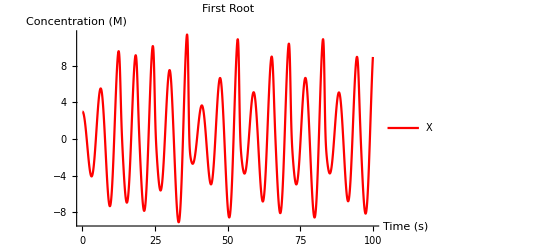

```mathematica
tmax=100;
sol=SimulateRxnsys[Join[CRNrossler,{conc[X1,4],conc[X2,1],conc[Y1,1],conc[Y2,1],conc[Z1,2],conc[Z2,2]}],tmax];
Plot[Evaluate[{X1[t]-X2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{X},
AxesLabel->{"Time (s)","Concentration (M)"},PlotLabel->"First Root"]
```

```mathematica
ParametricPlot3D[Evaluate[{X1[t]-X2[t],Y1[t]-Y2[t],Z1[t]-Z2[t]}/.sol],{t,0,tmax},PlotRange->{All,All,All},AxesLabel->{X,Y,Z}]
```

-Graphics3D-

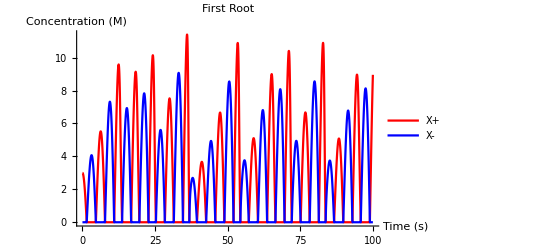

```mathematica
tmax=100;
sol=SimulateRxnsys[Join[CRNrossler,{conc[X1,4],conc[X2,1],conc[Y1,1],conc[Y2,1],conc[Z1,2],conc[Z2,2]}],tmax];
Plot[Evaluate[{X1[t],X2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{"X+","X-"},
AxesLabel->{"Time (s)","Concentration (M)"},PlotLabel->"First Root"]
```

```mathematica
soln:=NDSolve[{
x'[t]==-z[t]-y[t],
y'[t]==x[t]+a*y[t],
z'[t]==b+z[t]*(x[t]-c),
x[0]==3,
y[0]==0,
z[0]==0
},{x,y,z},{t,0,tmax}]
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotRange->{All,All,All},AxesLabel->{X,Y,Z}]
```

-Graphics3D-

Since for most of the plots, we are plotting the difference in the + and - components, the annihilation reaction speed that depends on k_fast doesn’t have any noticable effect. We only see an effect in the graph that plots both the + and - components, where both componenets grow very large. If we decrease the k_fast close to 0 then the plots seem to break.

## Part 2: Achieving the full range of algebraic expressions.

```mathematica
Clear[c];
```

```mathematica
CRNannihl[A1_,A2_,B1_,B2_,c1_,c2_]:={rxn[A1+A2,0,kf],rxn[B1+B2,0,kf],rxn[c1+c2,0,kf]}
```

I worked for >6 hours on this set and spend a couple hours just on inverse and division trying to test and figure out a way to do these functions. I was having some issues and they don’t work perfectly, but this is what I was able to complete without spending an unreasonable amount of time on this project. Unfortunately, I had done the most of the rest of the set earlier in the week except for the last few functions, and had other work so wasn’t able to go to office hours or get help. In the future, I’ll make sure to look through all the functions to make sure I get my questions answered earlier in the week.

They were all tested with negative and combination of positive and negative values, but only a single test is shown for each.
List of all modules that we are creating:

```mathematica
CRNconst[A1_,A2_,v_]:={rxn[0,A1,v],rxn[A1,0,1]}
CRNneg[A1_,A2_,B1_,B2_]:= {rxn[A1,A1+B2,1],rxn[A2,A2+B1,1],rxn[B1,0,1],rxn[B2,0,1]}
CRNcopy[A1_,A2_,B1_,B2_]:= {rxn[A1,A1+B1,1],rxn[A2,A2+B2,1],rxn[B1,0,1],rxn[B2,0,1 ]}
CRNadd[A1_,A2_,B1_,B2_,c1_,c2_]:={rxn[A1,A1+c1,1],rxn[A2,A2+c2,1],rxn[B1,B1+c1,1],rxn[B2,B2+c2,1],rxn[c1,0,1],rxn[c2,0,1]}
CRNsub[A1_,A2_,B1_,B2_,c1_,c2_]:={CRNneg[B1,B2,Bn1,Bn2],CRNadd[A1,A2,Bn1,Bn2,c1,c2]}
CRNmul[A1_,A2_,B1_,B2_,c1_,c2_]:={rxn[A1+B1,A1+B1+c1,1],rxn[A1+B2,A1+B2+c2,1],rxn[A2+B1,A2+B1+c2,1],rxn[A2+B2,A2+B2+c1,1],rxn[c1,0,1],rxn[c2,0,1]}
CRNinv[A1_,A2_,B1_,B2_]:= {rxn[0,B1,1],rxn[A1+B1,A1,1],rxn[B1,0,1],rxn[B2,0,1]}
CRNdiv[A1_,A2_,B1_,B2_,c1_,c2_]:= {CRNinv[B1,B2,Bn1,Bn2],CRNmul[A1,A2,Bn1,Bn2,c1,c2]}
CRNsquare[A1_,A2_,B1_,B2_]:={CRNmul[A1,A2,A1,A2,B1,B2]}
CRNsqrt[A1_,A2_,B1_,B2_]:={rxn[A1,A1+B1,1],rxn[B1+B1,0,1/2]}
```

CONST, i.e. A:= v, sets value to a positive constant. To get a negative constant, we can negate a positive constant.

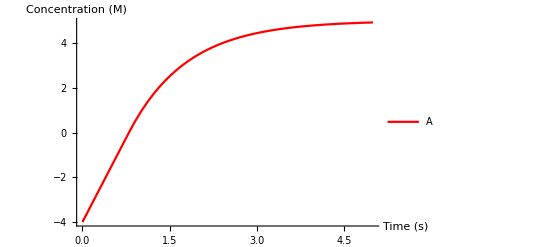

```mathematica
tmax=5;
v=5;
sol=SimulateRxnsys[{rxn[0,A1,v],rxn[A1,0,1],rxn[A1+A2,0,kf],conc[A1,0],conc[A2,4]},tmax];
Plot[Evaluate[{A1[t]-A2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green}},PlotLegends->{A},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{A1[tmax]-A2[tmax]}/.sol
```

{4.92502}

NEG, i.e. B:= -A

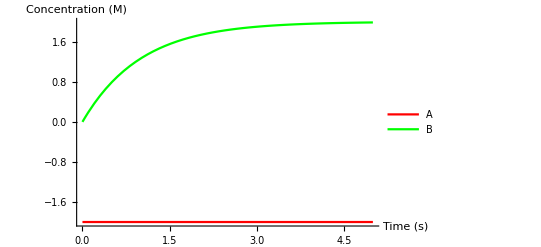

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A1,A1+B2,1],rxn[A2,A2+B1,1],rxn[B1,0,1],rxn[B2,0,1],conc[A1,5],conc[A2,7]},tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
B[tmax]/.sol
```

B[5]

COPY, i.e. B:= A,

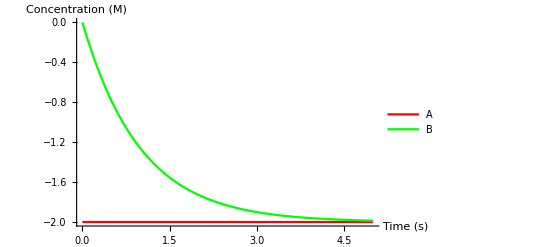

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A1,A1+B1,1],rxn[A2,A2+B2,1],rxn[B1,0,1],rxn[B2,0,1 ],conc[A1,5],conc[A2,7]},tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{B1[tmax]-B2[tmax]}/.sol
```

{-1.98652}

ADD, i.e. C= A+B

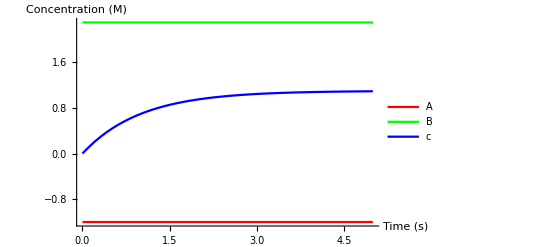

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A1,A1+c1,1],rxn[A2,A2+c2,1],rxn[B1,B1+c1,1],rxn[B2,B2+c2,1],rxn[c1,0,1],rxn[c2,0,1],conc[A1,1.4],conc[A2,2.6],conc[B1,3.6],conc[B2,1.3]},tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t],c1[t]-c2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{c1[tmax]-c2[tmax]}/.sol
```

{1.09259}

SUB, i.e. C= A-B

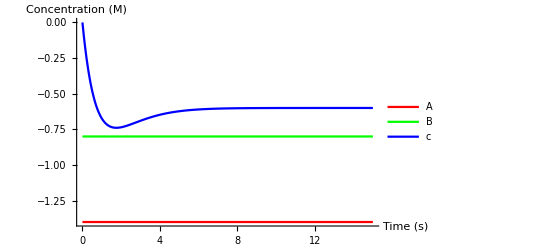

```mathematica
tmax=15;
rsys=Flatten[{CRNneg[B1,B2,Bn1,Bn2],CRNadd[A1,A2,Bn1,Bn2,c1,c2]}];
sol=SimulateRxnsys[Join[rsys,{conc[A1,1.4],conc[A2,2.8],conc[B1,2.6],conc[B2,3.4]}],tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t],c1[t]-c2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{c1[tmax]-c2[tmax]}/.sol
```

{-0.600003}

MUL, i.e. C:= A*B

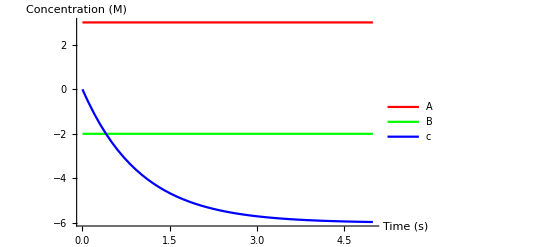

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A1+B1,A1+B1+c1,1],rxn[A1+B2,A1+B2+c2,1],rxn[A2+B1,A2+B1+c2,1],rxn[A2+B2,A2+B2+c1,1],rxn[c1,0,1],rxn[c2,0,1],conc[A1,5],conc[A2,2],conc[B1,3],conc[B2,5]},tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t],c1[t]-c2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
B[tmax]/.sol
```

B[5]

INV, i.e. B:= 1/A , seems to do 1/(A+1), tried a bunch of different options, but this worked the best of the things I tried.

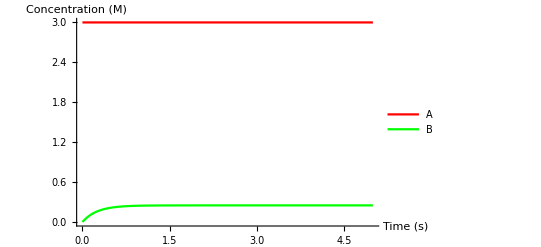

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[0,B1,1],rxn[A1+B1,A1,1],rxn[B1,0,1],rxn[B2,0,1],conc[A1,3],conc[A2,0]},tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{B1[tmax]-B2[tmax]}/.sol
```

{0.25}

DIV, i.e. C= A/B

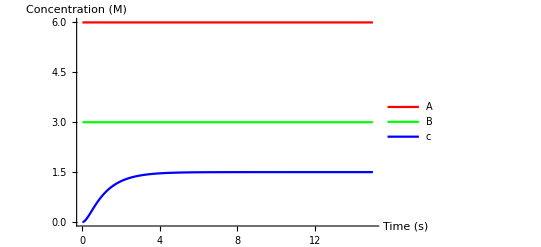

```mathematica
tmax=15;
rsys=Flatten[{CRNinv[B1,B2,Bn1,Bn2],CRNmul[A1,A2,Bn1,Bn2,c1,c2]}];
sol=SimulateRxnsys[Join[rsys,{conc[A1,6],conc[A2,0],conc[B1,3],conc[B2,0]}],tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t],c1[t]-c2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{c1[tmax]-c2[tmax]}/.sol
```

{1.5}

SQUARE, i.e. Z:= A^2

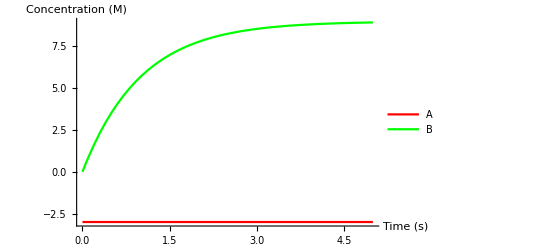

```mathematica
tmax=5;
rsys=Flatten[{CRNmul[A1,A2,A1,A2,B1,B2]}];
sol=SimulateRxnsys[Join[rsys,{conc[A1,2],conc[A2,5]}],tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{B1[tmax]-B2[tmax]}/.sol
```

{8.93936}

SQUAREROOT, i.e. Z:= √A

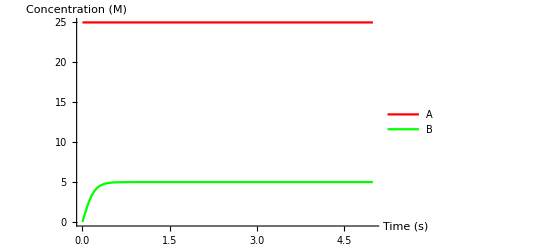

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A1,A1+B1,1],rxn[B1+B1,0,1/2],conc[A1,25],conc[A2,0],conc[B2,0]},tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{B1[tmax]-B2[tmax]}/.sol
```

{5.}

Quadratic roots

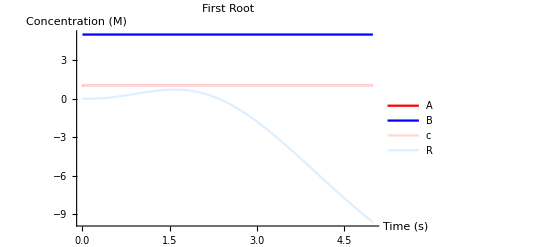

```mathematica
tmax=5;
rsys=Flatten[{CRNsquare[B1,B2,SB1,SB2],CRNconst[F1,F2,4],CRNmul[F1,F2,A1,A2,FA1,FA2],CRNmul[FA1,FA2,c1,c2,FAC1,FAC2],CRNsub[SB1,SB2,FAC1,FAC2,S1,S2],CRNsqrt[S1,S2,SQ1,SQ2],CRNadd[B1,B2,SQ1,SQ2,NUM1,NUM2],CRNconst[T1,T2,2],CRNmul[T1,T2,A1,A2,TA1,TA2],CRNdiv[NUM1,NUM2,TA1,TA2,R1,R2]}];
sol=SimulateRxnsys[Join[rsys,{conc[A1,1],conc[A2,0],conc[B1,5],conc[B2,0],conc[c1,1],conc[c2,0]}],tmax];
Plot[Evaluate[{A1[t]-A2[t],B1[t]-B2[t],c1[t]-c2[t],R1[t]-R2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{A,B,c,R},
AxesLabel->{"Time (s)","Concentration (M)"},PlotLabel->"First Root"]
```

```mathematica
{B=R1[tmax]-R2[tmax]}/.sol
```

{-9.62442}